```mathematica
SetDirectory["D:\\Qsync\\QOLab\\Data\\On Resonance Project\\Lab Book 2 (18 Mar 29 -)\\20-09-28\\Power\\87F22"];
data=Import[#]&/@FileNames["*csv"];
data2=Table[Take[data[[i]],{17,-2}],{i,1,Length[data]}];
SetDirectory["D:\\Qsync\\QOLab\\Data\\On Resonance Project\\Lab Book 2 (18 Mar 29 -)\\20-09-28\\Power\\87F22\\Off"];
dataoff=Import[#]&/@FileNames["*csv"];
data2off=Table[Take[dataoff[[i]],{17,-2}],{i,1,Length[dataoff]}];
```

```mathematica
f[data_]:=Module[{ll,max,min,yaxis1,yaxis2,wcn,ff,gg,loc,kk},
ll=data[[All,2]];
{max,min}=#[ll]&/@{Max,Min};
yaxis1=Take[data[[All,4]],Flatten[{#[ll,max][[1]],#[ll,min][[-1]]}&@Position]];
yaxis2=Take[data[[All,8]],Flatten[{#[ll,max][[1]],#[ll,min][[-1]]}&@Position]];

wcn=(794.76728224*10^-9);


ff[x_]:=Evaluate[Fit[


Flatten[{Table[{o,yaxis1[[o]]},{o,10,200}],Table[{o,yaxis1[[o]]},{o,Length[yaxis1]-200,Length[yaxis1]-10}]},1]

,{1,x},x]];
gg=Table[ff[x],{x,1,Length[yaxis1]}];
loc=Select[FindPeaks[
GaussianFilter[yaxis2,30]
,15,0.000001],1500<#[[1]]<5500&];
kk[x_]:=Evaluate[Fit[{{loc[[1,1]],-0.816},{loc[[-1,1]],0}},{1,x},x]];
{-12.531885282826405 wcn Log[yaxis1/gg],GaussianFilter[yaxis1/gg,10],yaxis2,Table[kk[x],{x,1,Length[yaxis1]}]}

]
```

```mathematica
Manipulate[
ListPlot[{GaussianFilter[data2[[i]][[All,8]],30],
Select[FindPeaks[
GaussianFilter[data2[[i]][[All,8]],30]
,15,0.000001],1500<#[[1]]<5500&]},PlotStyle->{Black,{Red,AbsolutePointSize[5]}}]
,{{i,22},1,Length[data2],1}]
```

```mathematica
Manipulate[ListPlot[Transpose[f[data2[[i]]][[{4,2}]]],PlotRange->{{-0.05,-0.02},{0.2,0.7}},Joined->True,Epilog->Line[{{-2,0.7},{2,0.68}}]],{{i,2},1,Length[data2],1}]
```

```mathematica
pw={0.5,1,2,3,4,5,6,7,8,9,10,15,20,25,30,35,40,50,60,70,80};power=Flatten[Transpose[{pw,pw,pw,pw}]];
EITmax8722=Table[
If[i<8,
Select[Transpose[f[data2[[i]]][[{4,2}]]],-0.04<#[[1]]<-0.02&][[All,2]]//Max,

Select[Transpose[f[data2[[i]]][[{4,2}]]],-0.05<#[[1]]<0.03&][[All,2]]//Max

],{i,1,Length[data],1}];
```

```mathematica
EITmin8722=Table[
If[i<8,
Select[Transpose[f[data2[[i]]][[{4,2}]]],-0.04<#[[1]]<-0.02&][[All,2]]//Min,

Select[Transpose[f[data2[[i]]][[{4,2}]]],-0.05<#[[1]]<0.03&][[All,2]]//Min

],{i,1,Length[data],1}];
```

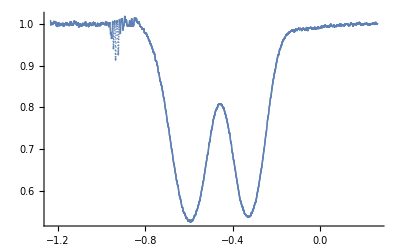

```mathematica
ListPlot[Transpose[f[data2off[[2]]][[{4,2}]]]]
```

```mathematica
Transpose[f[data2off[[2]]][[{4,2}]]][[All,2]]//Min
```

0.52577

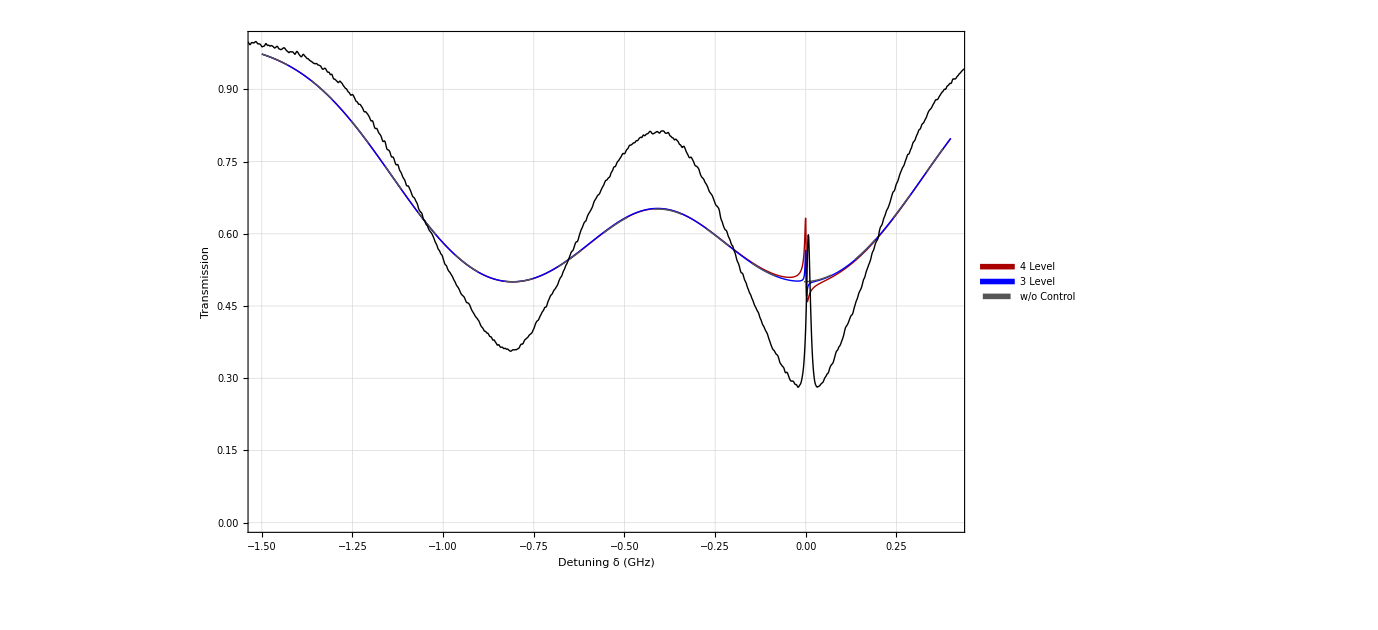

```mathematica
final2=ListPlot[{Lev4DoppTestsc[32,15/1000,0.9/1000,1.438*10^6,0*10^6,0],Lev3DoppTestsc[32,15/1000,0.9/1000,1.438*10^6,0*10^6,0],Lev3DoppTestsc[32,0/1000,1/1000,0.5*10^6,0*10^6,0]},Joined->True,FrameTicks->True,FrameTicksStyle->Directive[40],Frame->True,Axes->False,PlotLegends->Placed[legend,{Left,Bottom}],ImageSize->1020,PlotStyle-> {{AbsoluteThickness[1],Darker[Red]},{AbsoluteThickness[1],Blue},{AbsoluteThickness[1],Darker[Gray],Dashing[.02]},{AbsoluteThickness[1],Black,Dashed}},FrameLabel->{Style["Detuning δ (GHz)",50,Black],Style["Transmission ",50,Black]},GridLines->Automatic,PlotRange->{{-1.5,0.4},{0.0,1.0}}];
Show[final2,ListPlot[Transpose[f[data2[[46]]][[{4,2}]]],Joined->True,PlotStyle->{Thick,Black},Epilog->Line[{{-2,1},{2,1}}]]]
```

```mathematica
SetDirectory["D:\\Qsync\\QOLab\\Data\\On Resonance Project\\Lab Book 2 (18 Mar 29 -)\\20-09-28\\Power\\87F21\\Off"];
dataoff=Import[#]&/@FileNames["*csv"];
data2off=Table[Take[dataoff[[i]],{17,-2}],{i,1,Length[dataoff]}];
```

```mathematica
Table[Select[Transpose[f[data2off[[1]]][[{4,2}]]],-0.2<#[[1]]<+0.2&][[All,2]]//Min,{i,1,Length[dataoff],1}]//Mean
```

0.45656

```mathematica
Partition[EITmax8722,4]
```

{{0.406727,0.400049,0.415085,0.393683},{0.411684,0.419694,0.419887,0.460343},{0.428104,0.431248,0.434021,0.434431},{0.454455,0.471286,0.447428,0.456738},{0.499596,0.48124,0.494287,0.481763},{0.503174,0.497345,0.494714,0.488352},{0.512429,0.515817,0.508765,0.517356},{0.527694,0.534907,0.533498,0.530532},{0.543849,0.539972,0.537189,0.536623},{0.511488,0.555526,0.585209,0.548139},{0.567558,0.560733,0.56582,0.562971},{0.604176,0.597892,0.581878,0.59285},{0.624868,0.628613,0.625344,0.625365},{0.639249,0.639774,0.631689,0.63794},{0.655751,0.654082,0.618227,0.657655},{0.660993,0.653219,0.660565,0.662166},{0.67066,0.667739,0.667754,0.664614},{0.684851,0.682938,0.682973,0.684974},{0.696304,0.693762,0.696818,0.694026},{0.699255,0.699185,0.704246,0.70234},{0.711782,0.70706,0.711463,0.705317}}

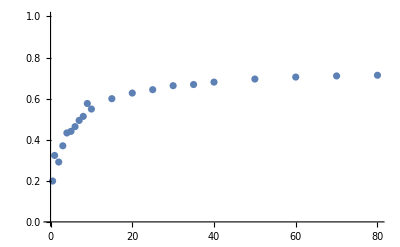

```mathematica
rb8722=ListPlot[{Transpose[{pw,1-Log[Max/@Partition[EITmax8722,4]]/Log[Max/@Partition[EITmin8722,4]]}]},PlotRange->{0,1}]
```

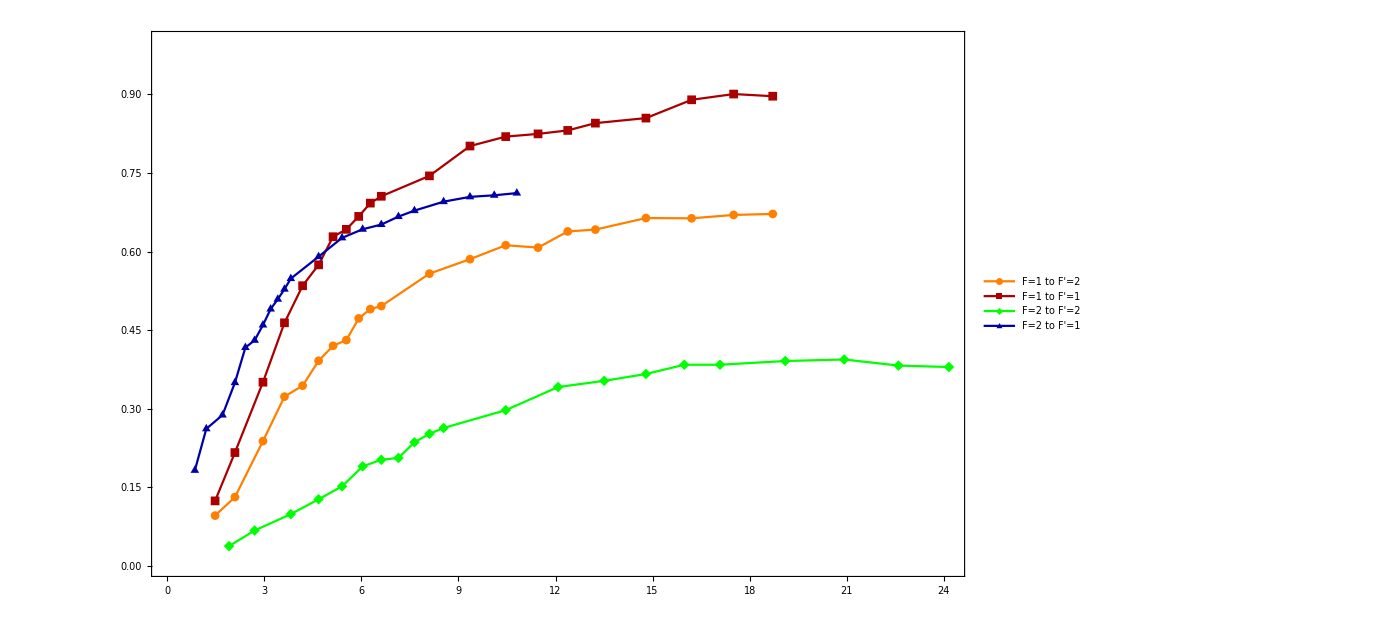

```mathematica
dd=ListPlot[{Transpose[{Rabi8722[pw/1000,0.9/1000],1-Log[Mean/@Partition[EITmax8711,4]]/Log[Mean/@Partition[EITmin8722,4]]}],Transpose[{Rabi8721[pw/1000,0.9/1000],1-Log[Mean/@Partition[EITmax8712,4]]/Log[Mean/@Partition[EITmin8712,4]]}],Transpose[{Rabi8712[pw/1000,0.9/1000],1-Log[Mean/@Partition[EITmax8721,4]]/Log[Mean/@Partition[EITmin8721,4]]}],Transpose[{Rabi8711[pw/1000,0.9/1000],1-Log[Mean/@Partition[EITmax8722,4]]/Log[Mean/@Partition[EITmin8722,4]]}]},PlotRange->{0,1},ImageSize->1020,PlotRange->{0,0.8},PlotLegends->{"F=1 to F'=2","F=1 to F'=1","F=2 to F'=2","F=2 to F'=1"},Joined->True,PlotMarkers->Automatic,MeshStyle->{Orange, Darker[Red],Green,Darker[Blue]},PlotStyle->{Orange, Darker[Red],Green,Darker[Blue]},Frame->True]
```

```mathematica
tr=ListPlot[{Tvw8722,Tvw8721,Tvw8711,Tvw8712},Joined->True,PlotLegends->{"F=1 to F'=2","F=1 to F'=1","F=2 to F'=1","F=2 to F'=2"},Joined->True,PlotStyle->{{Dashed,Orange}, {Dashed,Darker[Red]},{Dashed,Green},{Dashed,Darker[Blue]}},Frame->True]
```

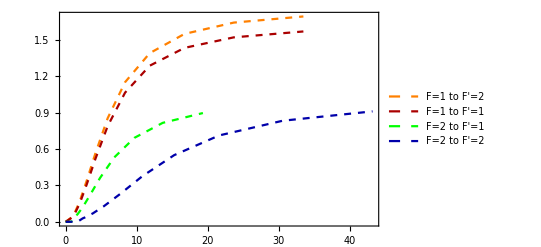
```mathematica
tr2=-Graphics-
```

-Graphics-

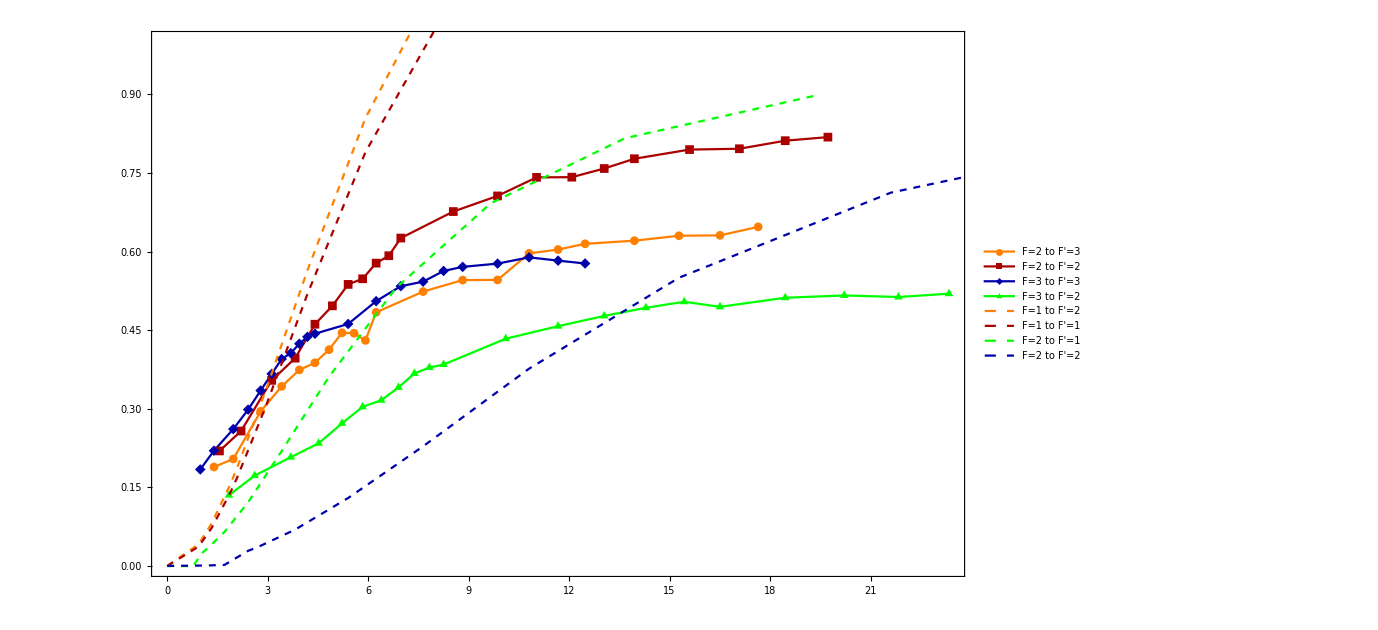

```mathematica
Show[dd,tr2]
```

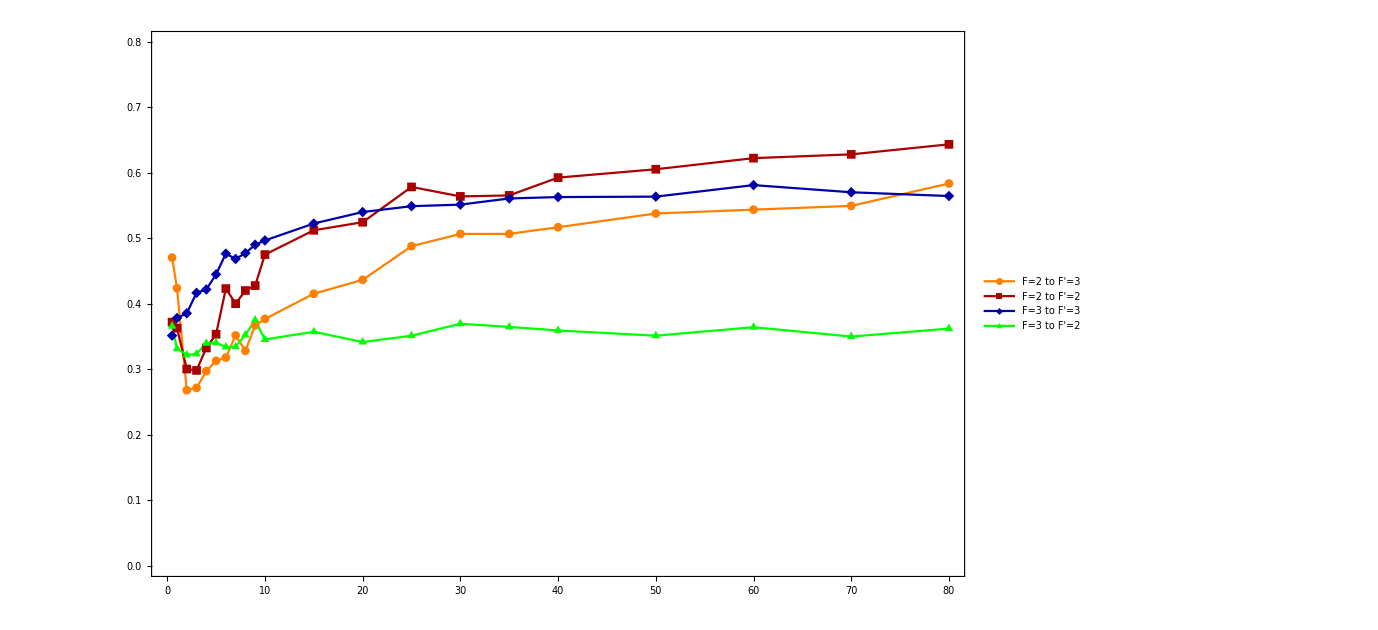

```mathematica
ListPlot[{Transpose[{pw,1-Log[Max/@Partition[EITmax7711,4]]/Log[0.48]}],Transpose[{pw,1-Log[Max/@Partition[EITmax7712,4]]/Log[0.7635754329884742]}],Transpose[{pw,1-Log[Max/@Partition[EITmax7721,4]]/Log[0.5469]}],Transpose[{pw,1-Log[Max/@Partition[EITmax7722,4]]/Log[0.5648711990304178]}]},ImageSize->1020,PlotRange->{0,0.8},PlotLegends->{"F=2 to F'=3","F=2 to F'=2","F=3 to F'=3","F=3 to F'=2"},Joined->True,PlotMarkers->Automatic,MeshStyle->{Orange, Darker[Red],Darker[Blue],Green},PlotStyle->{Orange, Darker[Red],Darker[Blue],Green},Frame->True]
```